```mathematica
(*
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
primeQp[n_]:=If[PrimeQ[n]&&n>0,True,False]
*)
```

## ( Template ) 15/12-‘19

### Thought

This is text.

#### Example

# Journal

/12-‘19

## 15/12-‘19

### Plan for 2020 (1)

I have to change my attitude/mindset: move from being a student to a qualified amateur researcher. A researcher has its own research program and plans and works accordingly. My first move has to be to define and write-up such a program.

## 16/12-‘19

### Plan for 2020 (2)

My field of interest is clearly Number Theory. For practice I want to do/collect a daily math.SE problem and follow AOPS/NT. Beyond that I want to study Analytic Number Theory, and write-up the material in my own ( to a group of peer-programmers level ) words.

#### Tasks

Start with the topic of Arithmetic Functions from different sources and angles. As long as it takes and staying focused. Prepare a LATEX document for the write-ups and use in first instance the Mathematica Notebook for notes and examples. I intend to start tomorrow with a scan of materials available.

## 17/12-‘19

### Daily Journal

Math.SE
https://math.stackexchange.com/questions/3472411/find-a-primitive-pythagorean-right-triangle-such-that-the-difference-of-two-shor
“I am asked to find a primitive Pythagorean triple (x,y,z) such that x2+y2=z2 and |x−y|=1, and x≥100 and y≥100.”

Perhaps I should include MathOverflow in the daily check.

#### Tasks

Added to MLO and currently working on:
- Scan Literature for Arithmetic Functions / Maak plan
- Plan Def. Study Calc - Mma
- Bouw Code for Riemann Prime Formula

## 18/12-‘19

### Daily Journal

Working on MoebiusMu, EulerPhi.
Orientating on a project about an extension for OpenOffice.
Started reading Robert Baillie’s paper on counting functions using Zeta. - First try to understand the summatory function of ϕ (EulerPhi ) which supposedly develops to x^2.

#### Tasks

- Understand the summatory function of ϕ

/5-‘20

## 18/5-‘20 Mo

### Daily Journal

Why did I quit the journal after only a few days? Can’t remember. My first notes and thoughts actually did inspire me and had a healing effect. Covid-19 or the Corona virus measurements helped me also. The all over “quiet-mode” in society helped me to relax and concentrate, so I have been quite productive.
Working on Apostol’s ANT mostly. Should/(want to) do more Riemann explorations and MMa programming projects.

### Snippets

```mathematica
Manipulate[
ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20Pi},PlotRange->1,PerformanceGoal->"Quality"],
Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2Pi},
Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2Pi}, ControlPlacement->Left]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20Pi},PlotRange->1.1,PerformanceGoal->"Quality",Axes -> axes,ImageSize -> size],
OpenerView[{"Horizontal",Column[{Control[{{n1,1,"Frequency"},1,4}],Control[{{a1,1,"Amplitude"},0,1}],Control[{{p1,0,"Phase"},0,2Pi}]},Right]}],OpenerView[{"Vertical",Column[{Control[{{n2,5/4,"Frequency"},1,4}],Control[{{a2,1,"Amplitude"},0,1}],Control[{{p2,0,"Phase"},0,2Pi}]},Right]}],OpenerView[{"Plot options",Row[{Control[{axes,{True,False}}],Control[{{size,Medium},{Small,Medium,Large}}]},Spacer[20]]}], ControlPlacement->Bottom]
```

```mathematica
Needs["Combinatorica`"]
```

## 21/5-‘20 Th

### Daily Journal

Recall to the extreme tiredness I must have had in the 90’s. - “Hemelvaartsdag.”

## 24/5-‘20 Su

### Daily Journal

R&D regarding finding the inverse of an arithmetical functions.
Are there more, better ways than the recursive method?
Is there a way to find a formula from the function generated with the recursive method?
What is the situation regarding functions that map numbers of the same prime signature to the same target? Is that rare?

### Snippets

```mathematica
ClearAll[f,g,h]
f[n_]:=PrimeNu[n]+Floor[1/n]
g[1]=1;
g[n_]:=g[n]=-1/f[1](Apply[Plus,Map[f[n/#]g[#]&,Most[Divisors[n]]]])
fg[n_]:=DivisorSum[n,f[#]g[n/#]&]
Table[{k,g[k]},{k,1,2}]//tf
```

```mathematica
parToNum[ls_]:=Apply[Times,MapIndexed[Prime[#2[[1]]]^#1&,ls]]
Table[Map[{#,g[parToNum[#]]}&,IntegerPartitions[k]],{k,0,7}]//tf
```

```mathematica
CoefficientList[Series[1/(1+x Exp[x]),{x,0,8}],x] Range[0,8]!
```

```mathematica
h[n_]:=Sum[(-1)^k k!k^(n-k)Binomial[n,k],{k,0,n}]
h[6]
```

### Weekplan

I will concentrate on the review of chapters 2,3 and 4, and study new topics in chapters 5 and 6.
Exercises-wise I will do work on chapter 2 and ( possibly ) exercises from Ram Murty.
To broaden the view I will read RH related books and gather ideas for further study and to create how-to’s.

## 25/5-‘20 Mo

### Daily Journal

OK. Learned something new today: the concept of Bell series. Not clear yet how Bell actually applied the series in his studies. I added a column “Bell Series” to the Arithmetical Functions Table. - I started, carefully, on the Keith Jordan L-Functions Note.

## 26/5-‘20 Tue

### Daily Journal

Continued, carefully, on the Keith Jordan L-Functions Note. - I must continue studying, start looking at modular forms and elliptic modular functions. - Can I organize the day/week in such a way that I can start studying multiple tracks?

## 28/5-‘20 Thu

### Daily Journal

OK. Finally got the Koukoupoloupos book The Distribution of Prime Numbers. - Anyway, it becomes clearer and clearer that there still is so much to do. - ( Prayer: ) I must stay on the road to the Proof of the PNT. It will take discipline and strength.

/6-‘20

## 1/6-‘20 Mo

### Daily Journal

Planning mostly, today, for a run to the PNT which is now in reach. Dimitri K.’s book will help here. - I have lost some excercise concentration lately. Must work on that tomorrow.

## 3/6-‘20 We

### Daily Journal

PNT is also part of  Heng Huat Chan’s book on ANT for undergraduates. Thát will be my first attack on the PNT. Found the Workbench again. I want to start ASAP with the work on my Number Theory package. Maybe I should “Zoom-In” in my MLO file while at the same time make room for other activities? - I found a topic I could publish about: Arithmetic Functions. - That also means reorganizing my Github space. - Tomorrow I want to do a “Laptop Cleanup”. - #A should be very high on the agenda too.

## 8/6-‘20 Mo

### Daily Journal

Testing... Workbench, etc.

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry`
```

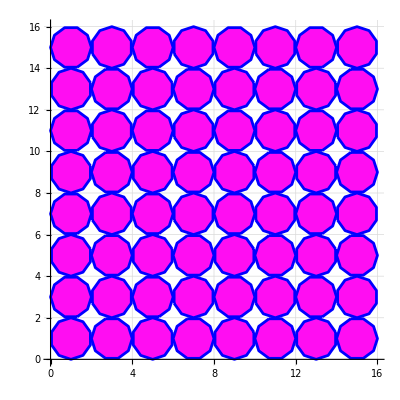

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[10,RGBColor[1,.05,.95,.1]][[1]],{1,1}],{Blue,1,.005,2 π,2 π}}
Nest[teil,dpoly,3]//toGL//gr1
```

Bought a new laptop Thursday. - Let’s	 think aloud people. - Where shall I put the package? - Do I have the Geometry package on Github already? - Yes, it is on Github, so all I have to do is check out how to update with Eclipse, and then develop numberTheory package in Geometry and focus from IntelliJ on the Arithmetic Functions paper. - Something like that.
ALERT: Where do all the PATHS come from in Geometry? UZT task!

And what a find is this.  <-- ( DirichletSeries coefficients from Zeta expression; what we have been looking for... )

## 10/6-‘20 We

### Daily Journal

With some problems ( but solved now ), I created an Eclipse workspace with Workbench Application project connected to a Github repository. So, I can now start developing the number theory package.
As below: the tf is now a function in the NumberTheory package.

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
Table[{m,m^2},{m,1,10}]//tf
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25
6 | 36
7 | 49
8 | 64
9 | 81
10 | 100

## 11/6-‘20 Th

### Daily Journal

Must concentrate on the Explicit Prime Counting Formula

## 13/6-‘20 Sa

### Daily Journal

Let’s try something...

```mathematica
hLine32[{{1,1},{2,3}}]
```

{{-5/2,4},(√85)/2,-ArcTan[6/7],-ArcTan[2/9],-5/2+4 ⅈ}

## 29/6-‘20 Mo

### Daily Journal

Yes. Will / must start working on the relation zeta-zeroes and prime-counting function. From there loopback to Apostol Ch3./Ch.4. Working hard on Arithmetical Functions. Purpose is to publish an expository paper on that subject. - Iets plannen om Riemann apart te behandelen? - B.v. 2 Projects Riemann Zeroes UZT / Arithmetic Functions Paper. - Not entirely sure, mensen.

/7-‘20

## |6/7-‘20 Mon

### Daily Journal

OK. Trying to follow along with Apostol’s proof of the PNT today. - // Living Geometry idea... is it still on?

## |7/7-‘20 Tue

### Daily Journal

? Flow: 6 Pomodori Math. Waarna langzaam de andere BLK’s gaan invullen. Véél hangt af van het volhouden in het Math. BLK.

## |10/7-‘20 Fri

Time to get started with Fourier Analysis / Transformations. 
I want to be able to handle Floor , Fraction functions in Integrals.
So what is a good way to learn Fourier Series ?

## |22/7-‘20 Wed

Since Sunday I am in a strange mood. Woke up in the middle of Saturday Night with the idea that I found a solution to the RH. Feeling somewhat stressed since. I can’t imagine that the proof is correct, but just to get it out of my system AND to practice a full proof write-up I decided to test the proof and write it up. If I publish I’ll see later.

/8-‘20

## |26/8-‘20 Wed

Nearly a month after my “RH cognition”... which lead to a two week long period of mania. - Twitter tells me that I woke up ( came back to reality ) on the 31st of July.
Since then I decided it is NOW the time to seriously start studying / investigating everything I could possibly find out and understand about the RH.
First blockage / cognition were the Modular Forms. A world lying before me, I just have to study, alongside Topology. MFOrms and TOPology are topics I’ll be studying in the forthcoming quarters.

/9-‘20

## 1/9-‘20 Tue

Time for a journal post. - Study of Elliptic Functions brought me to Lozano’s Elliptic Curves, Modular Forms and L-Functions. Having browsed that I suppose the way to go is to study Elliptic Curves for a while before I go back to Analytic Number Theory and the RH. The “Holmes Desk” now exists... but is rather empty. - ( I need doable problems. )

## 6/9-‘20 Sat

( I need doable problems. ) Yes! yES! - Therefore, after walkarounds and book searches, whatever, I decided to just take continue my efforts on Apostol I (ANT) and II (MFDS).

## 12/9-‘20 Sat

This week Mo - Sat ( Today ) was HARD. - From this I decided that my “condition” as a “sportsman” ( read: concentration / duration and proof skills as a mathematician ) is way below par. I need to go in training and build up condition. Clearly this includes changing food and drinking habits. For training I will revise Elementary NT and learn Quadratic NT as a step to Algebraic NT. - My first win is a certain level of awareness. I hope that I can continue this. - Need to figure out a Statistic for this.

## 14/9-‘20 Mon

My note from last Saturday was spot on. I want to hold on to this awareness. The focus on and ENT revision and QNT is good. Besides that I want to start doing some projects again, in the afternoons anyway. ( When that has become a habit I want to start focussing on ADMIN / FINANCE and INCOME, but that is besides this Journal. ) A very interesting project came up... build a MathLink connection between Mathematica and Pari GP. Through that I could Mathematica-Enable a lot of Pari GP functions. Why not? - I should not forget my ultimate goal; but I need practice, focus, concentration and contemplation.

## 15/9-‘20 Tue

Yes. I will start a project to use PariGP functions in Mathematica. ( It is quite a challenge, and hopefully, through it, I’ll be able to get my afternoons back. ) Today I continued studying QNT. Before I continue I must revise ( or DO ) Apostol ANT Chapter 9: Quadratic Residues and the Quadratic Reciprocity Law.

## 19/10-‘20 Mon

About the project to use PariGP functions in Mathematica... I kept on it. It is indeed a challenge. Hopefully, I can connect both PariGP and GAP. - It messed up my daily-structure considerably though. Initial stress, I suppose. - Slowly moving to a new pattern. I hope to do DEV in the morning and early afternoon. Then de “to-do-tjes”. And, ideally, in the evenings... Math Study. - Dear, dear, Lord, praying for this rythm.